```mathematica
Exit
```

```mathematica
DeleteDirectory["/Users/Henrik/github/CycleSamplerLink/LibraryResources/MacOSX-ARM64",DeleteContents->True]
```

```mathematica
Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

0.12608

0.106808

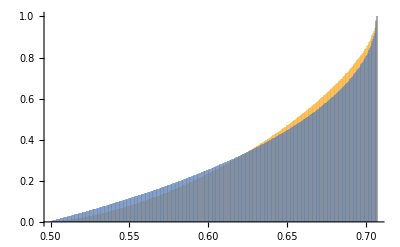

```mathematica
data1=CycleSample["Gyradius",3,ConstantArray[1,4],1000000,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSample["Gyradius",3,ConstantArray[1,4],1000000,"QuotientSpace"->True];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

Compiling cSampleChordLength[3]...

Compilation done. Time elapsed = 1.10828 s.

1.40791

0.111516

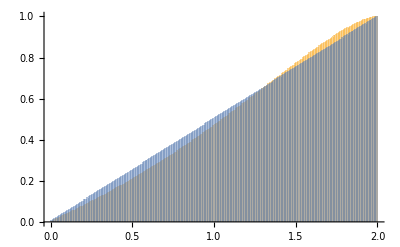

```mathematica
data1=CycleSampleChordLength[3,{1,1,1,1},{1,3},1000000,"QuotientSpace"->False];//AbsoluteTiming//First
data2=CycleSampleChordLength[3,{1,1,1,1},{1,3},1000000,"QuotientSpace"->True];//AbsoluteTiming//First
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

```mathematica
n=40;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
```

{0.498851,Null}

{0.525178,Null}

{0.493604,Null}

{0.542803,Null}

```mathematica
n=100;
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],1000000];//AbsoluteTiming
b=MomentPolytopeSample[n,1000000];//AbsoluteTiming
```

{1.0682,Null}

{2.34745,Null}

{1.15417,Null}

{2.36457,Null}

```mathematica
n=2000;
a=RandomClosedPolygons[3,ConstantArray[1.,n],10000];//AbsoluteTiming
b=MomentPolytopeSample[n,10000];//AbsoluteTiming
a=RandomClosedPolygons[3,ConstantArray[1.,n],10000];//AbsoluteTiming
b=MomentPolytopeSample[n,10000];//AbsoluteTiming
```

{0.225751,Null}

{6.97379,Null}

{0.199002,Null}

{7.1352,Null}